# f.figure.rencon2.strange.baryons-all.band.ed3.ci-1.5.nb

```mathematica
NotebookFileName[]
```

C:\octet.formfactor\f.figure.rencon2.strange.baryons-all.band.ed3.ci-1.5.nb

this nb is to record the all baryon octets ge gm experiment data and calculated data.

extract the Line data, and build the band

## note

增加曲线透明度选项，这样可以隐藏曲线

## initial

ge`charge: octet: 1 3 4 6, line, dash, dot, dot-dash

ge`neutral: octet: 2 5 7 8, line, dash, dot, dot-dash

** ** ** ** ** ** ** ** ** ** ** **

gm/μm`charge: octet: 1 3 4 6, line, dash, dot, dot-dash

gm/μm`neutral: octet: 2 5 7 8, line, dash, dot, dot-dash

```mathematica
directory`fig=FileNameJoin[{NotebookDirectory[],"/expression-fig/"}]
```

C:\octet.formfactor\expression-fig

## global setting

指定作图的ci值设定，1;;3,ci==1.0

```mathematica
data`instance=Span[4,6](*Span[4,6]*);
```

```mathematica
fontsize`frame=12;
imagesize=Scaled[.6];
```

```mathematica
fig`legend`magni=1;
```

默认的曲线间填充透明度

```mathematica
style`opacity=Opacity[0];
```

默认线宽

```mathematica
style`line`thick=Thickness[Medium];
```

线型,Dashing[{}]指定线为实线

```mathematica
style`line`type={Dashing[{}],Dashing[Medium],Dotted,DotDashed};
```

## import

## import origin figs

{Λ, ci}→

{0.8,1.0} l1c1,{0.9,1.0} l2c1,{1.0,1.0} l3c1,

{0.8,1.5} l1c2,{0.9,1.5} l2c2,{1.0,1.5} l3c2

```mathematica
fig`calc`baryons`ge`total`origin=
(
(Get[
FileNameJoin[{directory`fig,
#1
}
]
])&/@
{
(*+++++++++++++++++++++++++*)
"fig.calc.baryons.ge.tot.L-0.80.ci-1.0.m",
"fig.calc.baryons.ge.tot.L-0.90.ci-1.0.m",
"fig.calc.baryons.ge.tot.L-1.00.ci-1.0.m",

"fig.calc.baryons.ge.tot.L-0.80.ci-1.5.m",
"fig.calc.baryons.ge.tot.L-0.90.ci-1.5.m",
"fig.calc.baryons.ge.tot.L-1.00.ci-1.5.m"
}
);
```

```mathematica
fig`calc`baryons`gm`total`origin=(
(Get[
FileNameJoin[{directory`fig,
#1
}
]
])&/@
{
(*+++++++++++++++++++++++++*)
"fig.calc.baryons.gm.tot.L-0.80.ci-1.0.m",
"fig.calc.baryons.gm.tot.L-0.90.ci-1.0.m",
"fig.calc.baryons.gm.tot.L-1.00.ci-1.0.m",

"fig.calc.baryons.gm.tot.L-0.80.ci-1.5.m",
"fig.calc.baryons.gm.tot.L-0.90.ci-1.5.m",
"fig.calc.baryons.gm.tot.L-1.00.ci-1.5.m"
}
);
```

```mathematica
fig`calc`baryons`ge`total`origin//Dimensions
fig`calc`baryons`gm`total`origin//Dimensions
```

## extract data

```mathematica
{data`f1[x_],data`f1[y_]}^:=data`f2[Join[x,y]]
```

```mathematica
{data`f1[x_]}^:=data`f2[x]
```

将Line中出现的数据用data`f1做tag，并且通过赋上值的方式合并到data`f2

f 是format的意思

```mathematica
fun`data`extract[fig`calc`baryons`ge`total`origin_]:=Table[
Cases[
fig`calc`baryons`ge`total`origin⟦config,io,treeloop⟧
,Line[x_]:>data`f1[x],10(*level*)
]
,{config,1,6,1}
,{io,1,8,1}
,{treeloop,1,3,1}
]
```

```mathematica
data`calc`baryons`ge`total=fun`data`extract[fig`calc`baryons`ge`total`origin];
```

```mathematica
data`calc`baryons`gm`total=fun`data`extract[fig`calc`baryons`gm`total`origin];
```

```mathematica
data`calc`baryons`ge`total//Dimensions
data`calc`baryons`gm`total//Dimensions
```

## regularize data

```mathematica
{data`rearrange`ge,data`rearrange`gm}=(Transpose[
#1,
{3,1,2}
]&)/@{
data`calc`baryons`ge`total,data`calc`baryons`gm`total
};
```

```mathematica
data`rearrange`ge//Dimensions
data`rearrange`gm//Dimensions
```

## draw

## initial

给定颜色和线型方案，带电粒子4个，中性粒子4个，同样的排列

```mathematica
style`exp={
AbsoluteThickness[_]-> AbsoluteThickness[.8],
PointSize[_]->PointSize[0.02]
};
```

定义用到的颜色方案，带电粒子4个，中性粒子4个，是相同的

mma 默认的图形颜色

```mathematica
color`default = RGBColor[0.368417, 0.506779, 0.709798];
```

1,3,4,6;2,5,7,8

```mathematica
style`colors`theme={Blue,Green,Red,Black};
```

```mathematica
style`colors = {
(*1*)style`colors`theme⟦1⟧,
(*2*)style`colors`theme⟦1⟧,
(*3*)style`colors`theme⟦2⟧,
(*4*)style`colors`theme⟦3⟧,
(*5*)style`colors`theme⟦2⟧,
(*6*)style`colors`theme⟦4⟧,
(*7*)style`colors`theme⟦3⟧,
(*8*)style`colors`theme⟦4⟧
};
```

线型和颜色组合

```mathematica
fun`style`line[a_,b_,c_]:=Directive[style`line`thick,style`line`type⟦a⟧,style`colors`theme⟦b⟧,Opacity[c]]
```

设定八重态曲线style

```mathematica
style`line={

(*1*){fun`style`line[1,1,0],fun`style`line[1,1,1],fun`style`line[1,1,0]},
(*2*){fun`style`line[1,1,0],fun`style`line[1,1,1],fun`style`line[1,1,0]},
(*3*){fun`style`line[2,2,0],fun`style`line[2,2,1],fun`style`line[2,2,0]},
(*4*){fun`style`line[3,3,0],fun`style`line[3,3,1],fun`style`line[3,3,0]},
(*5*){fun`style`line[2,2,0],fun`style`line[2,2,1],fun`style`line[2,2,0]},
(*6*){fun`style`line[4,4,0],fun`style`line[4,4,1],fun`style`line[4,4,0]},
(*7*){fun`style`line[3,3,0],fun`style`line[3,3,1],fun`style`line[3,3,0]},
(*8*){fun`style`line[4,4,0],fun`style`line[4,4,1],fun`style`line[4,4,0]}
};
```

设置填充颜色和透明度

```mathematica
style`filling=Table[
{
1->{{2},Directive[style`opacity,style`colors⟦io⟧]},
3->{{2},Directive[style`opacity,style`colors⟦io⟧]}
}
,{io,1,8,1}
];
```

设置图例样式

```mathematica
style`legend={
Directive[Dashing[{}],style`colors`theme⟦1⟧],
Directive[Dashing[Medium],style`colors`theme⟦2⟧],
Directive[Dotted,style`colors`theme⟦3⟧],
Directive[DotDashed,style`colors`theme⟦4⟧]
};
```

设置框架样式

```mathematica
style`frame={
{
Directive[AbsoluteThickness[0.8],FontSize->fontsize`frame,Black],
Directive[AbsoluteThickness[0.8],FontSize->fontsize`frame,Black]
},
{
Directive[AbsoluteThickness[0.8],FontSize->fontsize`frame,Black],
Directive[AbsoluteThickness[0.8],FontSize->fontsize`frame,Black]
}
};
```

## functions to draw

fig`rearrange`ge,fig`rearrange`gm:

{io,treeloop,Λ`ci},{8,3,6}

Λ`ci:{0.80,1.0},{0.90,1.0},{1.00,1.0}

{0.80,1.5},{0.90,1.5},{1.00,1.5}

**********************************

此函数产生带状图

```mathematica
(*io=8;*)treeloop=3;
fig`baryons`band[
data`rearrange_(*the fig data extracted*)
]:=Table[
ListLinePlot[
data`rearrange⟦io,treeloop,data`instance⟧/.{data`f2->Sequence},
PlotStyle->style`line⟦io⟧,
Filling->style`filling⟦io⟧,
PlotRange->Full
]
,{io,1,8,1}
];
```

ge`charge: octet: 1 3 4 6, line, Dashing, Dotted, DotDashed

fig`calc`baryons`ge`total⟦octet,tree-loop-total⟧

横纵轴线标记

```mathematica
framelabel`ge={
{Style["G_E^B(Q^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None},
{Style["Q^2(GeV^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None}
};
```

```mathematica
framelabel`gm={
{Style["G_M^B(Q^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None},
{Style["Q^2(GeV^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None}
};
```

对图形的细节进行调整

```mathematica
fun`fig`gegm`cn[
fig`baryons`band_,(*function, generate band figure using data of ge or gm *)
framelabel_,(*framelabel of ge or gm*)
legend`text_,(*legend text*)
legend`ps_:legend`position(*legend position*)
]:=Legended[
Show[
(Sequence@@fig`baryons`band),
ImageSize->Large,
PlotRange->All,
PlotRangePadding->{{0,0},{Scaled[0.09],Scaled[0.09]}},
Frame->True,
FrameStyle->style`frame,
FrameLabel->framelabel
],
(*++++++++++++++++++++++++++++++*)
Placed[
Style[
LineLegend[{
style`legend⟦1⟧,style`legend⟦2⟧,
style`legend⟦3⟧,style`legend⟦4⟧
},
(Style[#1,FontFamily->"Times New Roman",FontSize->12]&)/@legend`text
(*,LegendFunction->Framed*)
],
Magnification->fig`legend`magni
],
legend`ps
]
];
```

## fun apply

### ge`charge

fun`fig`gegm`cn[
 fig`baryons`band_,(*function, generate band figure using data of ge or gm *)
 framelabel_,(*framelabel of ge or gm*)
 legend`text_,(*legend text*)
 legend`ps_: legend`position(*legend position*)
 ]

legend text and legend position

```mathematica
legend`t1={"Σ^-","Σ^+","p","Ξ^-"};
```

```mathematica
legend`ps1={
{0.03,0.3},
{0.,0.}
};
```

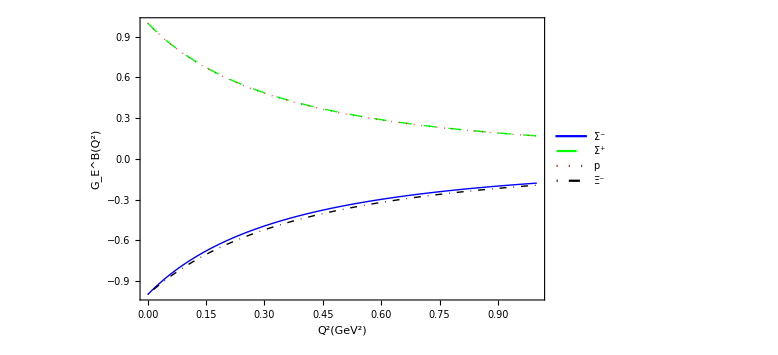

```mathematica
fig`baryons`ge`charge=fun`fig`gegm`cn[
fig`baryons`band[data`rearrange`ge]⟦{1,3,4,6}⟧,
framelabel`ge,
legend`t1,
legend`ps1
]
```

### ge`neutral

legend text and legend position

```mathematica
legend`t2={"Σ^0","n","Ξ^0","Λ"};
```

```mathematica
legend`ps2= {
  {0.03, 0.70},(*anchor position*)
  {0.,0.}(*legend anchor*)
  };
```

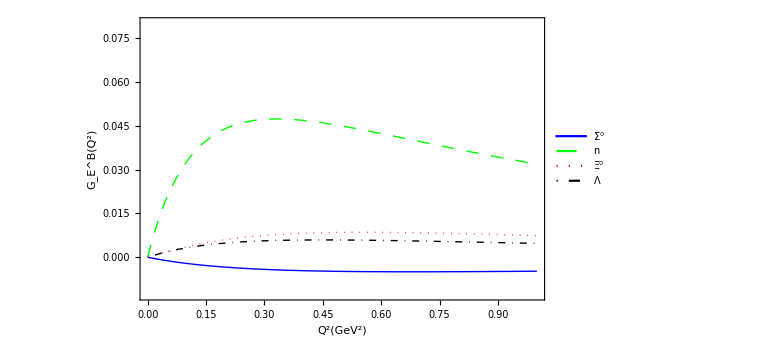

```mathematica
fig`baryons`ge`neutral=fun`fig`gegm`cn[
fig`baryons`band[data`rearrange`ge]⟦{2,5,7,8}⟧,
framelabel`ge,
legend`t2,
legend`ps2
]
```

### gm`charge

gm`charge: octet: 1 3 4 6, line, Dashing, Dotted, DotDashed

legend`t1={"Σ^-","Σ^+","p","Ξ^-"};

```mathematica
legend`ps3= {
  {0.03, 0.03},(*anchor position*)
  {0.,0.}(*legend anchor*)
  };
```

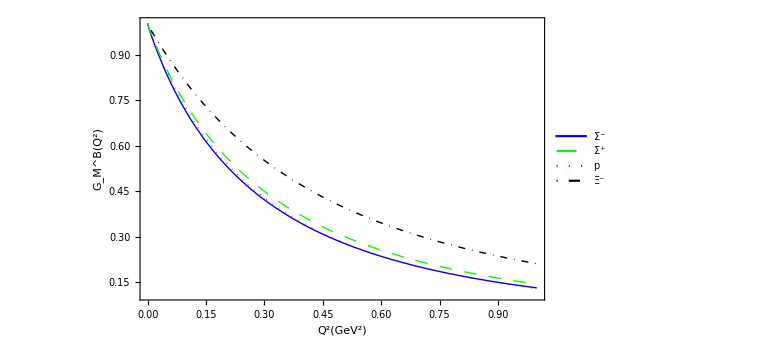

```mathematica
fig`baryons`gm`charge=fun`fig`gegm`cn[
fig`baryons`band[data`rearrange`gm]⟦{1,3,4,6}⟧,
framelabel`gm,
legend`t1,
legend`ps3
]
```

### gm`neutral

gm`neutral: octet: 2 5 7 8, line, Dashing, Dotted, DotDashed

legend`t2={"Σ^0","n","Ξ^0","Λ"};

```mathematica
legend`ps4= {
  {0.03, 0.03},(*anchor position*)
  {0.,0.}(*legend anchor*)
  };
```

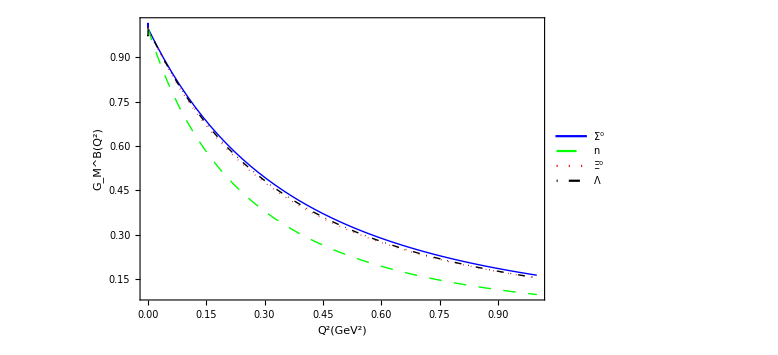

```mathematica
fig`baryons`gm`neutral=fun`fig`gegm`cn[
fig`baryons`band[data`rearrange`gm]⟦{2,5,7,8}⟧,
framelabel`gm,
legend`t2,
legend`ps4
]
```

## export

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"/expression-results/"}]]
```

C:\octet.formfactor\expression-results

```mathematica
Export["fig`baryons`ge`charge.ed3.ci-1.5.pdf",fig`baryons`ge`charge];
Export["fig`baryons`ge`neutral.ed3.ci-1.5.pdf",fig`baryons`ge`neutral];
```

```mathematica
Export["fig`baryons`gm`charge.ed3.ci-1.5.pdf",fig`baryons`gm`charge];
Export["fig`baryons`gm`neutral.ed3.ci-1.5.pdf",fig`baryons`gm`neutral];
```